```mathematica
Quit[]
```

```mathematica
<<Toolbox`
<<Toolbox`Style`
SetDirectory[NotebookDirectory[]];

enzModelsDir = "/home/mrama/Dropbox/MASSef/examples/"
mainDir=enzModelsDir<>"code_data/";
Import[mainDir<>"sim_plot_functions.m"];
Import[mainDir<>"simulation.m"];
```

/home/mrama/Dropbox/MASSef/examples/

## Simulations

### Systematic simulations

```mathematica
modelList=Import["/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/output/model_simulations/models/model_FBP2_all_0.mx"];
```

```mathematica
maxTimeConstants=Table[

jacobian=getJacobian[modelList[[ind]]]/.stripUnits[modelList[[ind]]["InitialConditions"]]/.stripUnits[modelList[[ind]]["Parameters"]];

Max[1/Abs[Re@Eigenvalues[jacobian]]],

{ind,1,Length@modelList}];
```

```mathematica
maxTimeConstants
```

{9.47348×10^20,6.05806×10^18,2.36069×10^10,1.70713×10^13,8.21923×10^15,2.27271×10^20,-1.09994×10^-9,1.06586×10^16,9434,9.74742×10^19,2.89026×10^17,2.49049×10^17,1.26112×10^14,8.09589×10^8,2.78342×10^9,1.5369×10^12,7.71986×10^21}
 |  |  |  |

```mathematica
ind=7;
jacobian=getJacobian[modelList[[ind]]]/.stripUnits[modelList[[ind]]["InitialConditions"]]/.stripUnits[modelList[[ind]]["Parameters"]];
Sort[1/Eigenvalues[jacobian]]
```

{-2.14123×10^16,-2.14123×10^16,-2.8712×10^8,-1.8035×10^6,-0.0000930665,-9.82999×10^-6,-3.8504×10^-6,-2.63884×10^-8,-1.12413×10^-9,-1.09994×10^-9}

```mathematica
Select[maxTimeConstants, #<10^1&]
```

{}

```mathematica
maxTimeConstants[[7]]
```

-1.09994×10^-9

```mathematica
Flatten@Map[Position[maxTimeConstants,#]&,Select[maxTimeConstants, #<10^1&]]
```

{7,21,26,28,38,49,73,93,129,132,133,139,149,159,167,175,196,212,222,225,227,248,256,266,276,278,284,286,309,312,316,317,318,319,321,322,327,332,340,348,351,352,356,358,370,380,385,390,404,406,412,435,443,463,473,481,483,516,542,543,544,546,548,554,565,577,580,586,599,605,626,628,631,644,650,664,682,688,699,722,732,733,740,760,768,781,792,794,814,822,826,829,858,859,864,868,875,880,906,907,914,918,926,936,957,962,964,965,966,968,969,975,986,988,994,995,1012,1017,1026,1036,1073,1078,1101,1113,1118,1125,1128,1173,1200,1202,1221,1231,1233,1239,1242,1247,1263,1267,1270,1275,1290,1298,1300,1334,1344,1345,1351,1361,1363,1368,1370,1388,1389,1395,1396,1400,1402,1406,1407,1412,1438,1439,1441,1444,1450,1454,1457,1469,1480,1485,1488,1496,1501,1507,1510,1563,1568,1572,1617,1618,1630,1656,1659,1665,1670,1671,1680,1683,1693,1703,1712,1723,1744,1756,1760,1766,1784,1785,1786,1789,1798,1800,1803,1809,1816,1825,1832,1843,1846,1872,1876,1910,1917,1923,1933,1937,1939,1952,1983,1989,1990,1994,2004,2006,2021,2022,2030,2032,2039,2044,2050,2053,2055,2061,2066,2129,2144,2157,2159,2169,2179,2183,2230,2261,2268,2275,2297,2298,2304,2305,2317,2328,2351,2370,2403,2412,2426,2428,2432,2433,2443,2448,2449,2457,2493,2494,2499,2506,2519,2522,2527,2542,2544,2546,2547,2574,2579,2589,2599,2600,2616,2617,2630,2632,2636,2639,2640,2641,2647,2655,2661,2665,2672,2679,2703,2711,2716,2740,2743,2749,2754,2788,2807,2818,2823,2829,2840,2845,2848,2857,2860,2862,2877,2878,2884,2894,2908,2924,2929,2941,2960,2963,2965,2966,2969,2973,2981,2987,3003,3009,3013,3021,3023,3034,3037,3040,3047,3066,3069,3084,3087,3088,3097,3106,3112,3123,3127,3131,3135,3161,3165,3168,3173,3174,3187,3203,3215,3217,3228,3235,3239,3242,3251,3259,3267,3271,3273,3275,3278,3283,3286,3291,3300,3304,3306,3307,3308,3318,3320,3322,3349,3357,3359,3377,3379,3384,3393,3398,3399,3403,3411,3416,3425,3426,3432,3436,3438,3441,3442,3455,3467,3471,3473,3489,3490,3491,3498,3513,3525,3528,3537,3539,3543,3547,3558,3560,3562,3570,3571,3576,3587,3588,3595,3596,3612,3631,3654,3670,3671,3672,3684,3693,3709,3711,3724,3742,3746,3751,3771,3788,3793,3796,3800,3813,3818,3819,3844,3845,3849,3852,3873,3875,3876,3885,3886,3901,3906,3908,3920,3927,3932,3933,3940,3952,3961,3972,3983,4004,4017,4040,4055,4062,4076,4080,4084,4108,4116,4117,4121,4126,4127,4132,4135,4149,4159,4175,4177,4181,4184,4191,4201,4202,4208,4209,4261,4265,4273,4289,4295,4322,4329,4332,4361,4369,4375,4377,4384,4391,4421,4427,4428,4431,4432,4433,4439,4448,4455,4457,4465,4469,4480,4488,4491,4493,4497,4505,4510,4512,4514,4515,4525,4548,4553,4554,4560,4561,4565,4573,4585,4591,4601,4602,4614,4616,4621,4623,4625,4631,4646,4647,4654,4660,4661,4665,4698,4706,4744,4748,4753,4771,4772,4774,4775,4791,4794,4799,4827,4833,4854,4857,4858,4870,4875,4903,4911,4932,4946,4977,4981,4988,4990,4995,4996,5018,5029,5034,5040,5042,5048,5056,5065,5128,5131,5137,5138,5139,5142,5167,5172,5173,5188,5222,5223,5226,5231,5233,5254,5263,5264,5277,5287,5288,5295,5296,5301,5305,5306,5316,5319,5352,5363,5366,5372,5388,5409,5418,5425,5431,5447,5454,5459,5461,5466,5477,5490,5495,5501,5502,5512,5515,5528,5537,5546,5552,5561,5573,5585,5592,5601,5602,5608,5635,5641,5646,5647,5648,5674,5678,5680,5684,5696,5702,5754,5769,5770,5786,5814,5827,5832,5837,5844,5851,5856,5857,5861,5882,5888,5893,5916,5918,5927,5931,5944,5946,5952,5954,5960,5962,5971,6007,6018,6023,6033,6038,6049,6059,6074,6077,6088,6090,6101,6117,6121,6126,6138,6139,6142,6146,6160,6201,6203,6229,6239,6256,6262,6265,6268,6274,6279,6289,6306,6314,6320,6331,6336,6345,6374,6376,6383,6388,6399,6400,6405,6415,6422,6426,6428,6432,6461,6463,6470,6473,6481,6483,6492,6494,6501,6509,6520,6528,6551,6555,6580,6588,6603,6610,6637,6644,6646,6649,6653,6657,6666,6674,6676,6683,6685,6697,6700,6709,6716,6718,6726,6738,6749,6750,6753,6759,6761,6767,6774,6782,6785,6794,6800,6807,6816,6818,6820,6846,6865,6868,6871,6872,6884,6913,6924,6925,6929,6936,6947,6970,6983,6984,7008,7013,7015,7017,7023,7034,7038,7049,7056,7068,7096,7103,7110,7118,7134,7137,7141,7156,7167,7175,7186,7192,7199,7205,7209,7236,7238,7252,7255,7263,7266,7268,7300,7307,7308,7316,7329,7342,7377,7407,7415,7431,7437,7443,7446,7447,7448,7470,7471,7481,7489,7505,7510,7520,7530,7535,7537,7549,7559,7560,7562,7588,7612,7638,7659,7664,7673,7675,7679,7685,7690,7691,7699,7725,7736,7737,7772,7783,7788,7795,7799,7800,7823,7830,7835,7841,7842,7844,7848,7875,7901,7905,7906,7928,7935,7940,7955,7961,7962,7964,7977,7979,7987,8003,8009,8026,8028,8044,8049,8051,8058,8062,8067,8072,8104,8108,8112,8117,8118,8138,8142,8167,8171,8177,8183,8194,8210,8211,8219,8247,8256,8257,8262,8263,8281,8284,8290,8291,8314,8321,8337,8343,8355,8360,8361,8369,8370,8373,8383,8384,8390,8400,8418,8425,8441,8443,8448,8470,8471,8479,8483,8505,8519,8524,8530,8544,8549,8562,8566,8568,8573,8576,8586,8619,8630,8632,8633,8636,8642,8669,8677,8678,8704,8707,8714,8717,8722,8735,8750,8756,8761,8778,8779,8780,8785,8787,8796,8799,8806,8816,8826,8828,8833,8838,8842,8850,8863,8872,8884,8885,8887,8894,8899,8902,8912,8916,8924,8931,8937,8943,8950,8959,8965,8973,8980,8988,9001,9004,9008,9015,9023,9029,9030,9039,9043,9076,9106,9107,9118,9129,9153,9157,9158,9162,9169,9173,9178,9192,9198,9201,9205,9208,9211,9222,9225,9248,9258,9259,9274,9276,9284,9289,9299,9313,9326,9329,9332,9333,9340,9343,9352,9368,9374,9375,9376,9383,9385,9393,9403,9406,9412,9414,9418,9436,9439}

```mathematica
BoxWhiskerChart[maxTimeConstants]
```

-Graphics-

```mathematica
Re@Eigenvalues[jacobian]
```

{-2.57637×10^9,-9.74759×10^8,-8.89828×10^8,-3.66456×10^8,-1.52845×10^7,-4794.71,-3.32427×10^-6,-3.52988×10^-8,5.85779×10^-14,5.85779×10^-14}

```mathematica
{conc, flux}=simulate[modelList[[7]],{t,0,10},InitialConditions-> {fdp^c-> 0.1}];
```

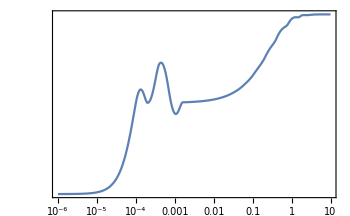

```mathematica
plotSimulation[FilterRules[flux, Subscript[v, FBP25]], {t,0,10}]
```

```mathematica
Sort@Values@FilterRules[modelList[[1]]["Parameters"],{Subscript[k, FBP21]^⟶,Subscript[k, FBP22]^⟶,Subscript[k, FBP23]^⟶,Subscript[k, FBP24]^⟶,Subscript[k, FBP25]^⟶,Subscript[k, FBP26]^⟶,Subscript[k, FBP27]^⟶,Subscript[k, FBP21]^⟵,Subscript[k, FBP22]^⟵,Subscript[k, FBP23]^⟵,Subscript[k, FBP24]^⟵,Subscript[k, FBP25]^⟵,Subscript[k, FBP26]^⟵,Subscript[k, FBP27]^⟵}]
```

{1.09152×10^-6,11.7928,309.715,37282.2,443420.,8.59438×10^8,9.23705×10^8,9.70147×10^8,9.99928×10^8,9.99999×10^8,9.99999×10^8,9.99999×10^8,1.×10^9,1.×10^9}

```mathematica
Times@@Values@FilterRules[modelList[[1]]["Parameters"],{Subscript[k, FBP21]^⟶,Subscript[k, FBP22]^⟶,Subscript[k, FBP23]^⟶,Subscript[k, FBP24]^⟶,Subscript[k, FBP25]^⟶,Subscript[k, FBP26]^⟶,Subscript[k, FBP27]^⟶}]
```

1.45132×10^45

```mathematica
(Times@@Values@FilterRules[modelList[[1]]["Parameters"],{Subscript[k, FBP21]^⟶,Subscript[k, FBP22]^⟶,Subscript[k, FBP23]^⟶,Subscript[k, FBP24]^⟶,Subscript[k, FBP25]^⟶,Subscript[k, FBP26]^⟶,Subscript[k, FBP27]^⟶}])/
(Times@@Values@FilterRules[modelList[[1]]["Parameters"],{Subscript[k, FBP21]^⟵,Subscript[k, FBP22]^⟵,Subscript[k, FBP23]^⟵,Subscript[k, FBP24]^⟵,Subscript[k, FBP25]^⟵,Subscript[k, FBP26]^⟵,Subscript[k, FBP27]^⟵}])
```

41.5

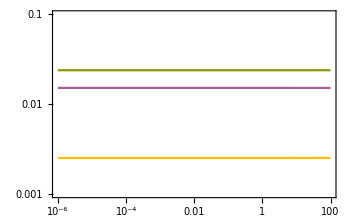

```mathematica
tFinal=100;
{conc,flux}=simulate[modelList[[1]],{t,0,tFinal}];
plotSimulation[conc,{t,0,tFinal}, PlotRange-> {{0,tFinal},{0.001, 0.1}}]
```

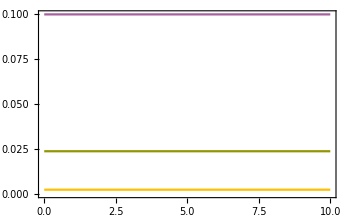

```mathematica
plotSimulation[conc,PlotFunction-> Plot, PlotRange-> {{0,10},{10^-4,10^-1}}]
```

```mathematica
enzName="FBP2";
inputDir = enzModelsDir<>"FBP2/fit_FBP2/output/model_simulations/models/";
outputDirBase = enzModelsDir<>"FBP2/fit_FBP2/output/model_simulations/data/";
If[!DirectoryQ[outputDirBase],
	CreateDirectory[outputDirBase,CreateIntermediateDirectories-> True]
];

headerConcMets={ "fdp", "f6p","pi"};
headerConcEnz={"FBP2","FBP2&fdp","FBP2&pi","FBP2&fdp&fdp","FBP2&pi&pi","FBP2&pi&pi&f6p","FBP2&pi&pi&f6p&f6p"};
headerFlux={"v_FBP21","v_FBP22","v_FBP23","v_FBP24","v_FBP25","v_FBP26","v_FBP27"};
subInd = {9};
prodInd={8,10};
indEnz={1, 2,3,4,5,6,7};

initCondList={};
outputDirList={"noPerturb"};


tValues=Map[10^#&,Range[-6,3, 0.1]];
tFinal=1000;
tValues=Insert[tValues,0., 1];


modelIDList={"all_100"};
nModelEnsembles={1,3};

 

outputDir =outputDirBase;
If[!DirectoryQ[outputDir<>"/data_mx/"],
	CreateDirectory[outputDir<>"/data_mx/",CreateIntermediateDirectories-> True]
];
```

```mathematica
Do[

simulateEnsembleNoCheck[inputDir, outputDir, enzName, modelID, nModelEnsembles, tFinal, tValues, initCondList, headerConcEnz, headerConcMets, headerFlux, indEnz,subInd, prodInd];,

{modelID, modelIDList}];
```

/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/output/model_simulations/models/model_FBP2_all_100_1.mx

/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/output/model_simulations/models/model_FBP2_all_100_2.mx

/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/output/model_simulations/models/model_FBP2_all_100_3.mx